# QPU Service Connection

The Wolfram Quantum Framework is a toolkit for Wolfram Language that offers quantum simulations. The Framework brings quantum experimentation to anyone and opens the door for more research and development of quantum algorithms.

This can also be used to connect with external cloud services such as IBM Quantum for an even closer look at what running on quantum hardware could be.

```mathematica
<<Wolfram`QuantumFramework`
```

## First time users

Connections to external services (such as quantum hardware access) can be utilized by establishing a service connection.

### IBM-Quantum Connection

If you want to use an IBM backend, create an IBM Quantum account. To create a new connection to IBMQ, you can use the following code:

```mathematica
ibmq=ServiceConnect["IBMQ","New"]
```

ServiceObject[…]

The first time you attempt to connect to a service that requires an API token, you will see the following window appear:

If you choose to save the connection, you can simply use ServiceConnect[“IBMQ”] the next time that you want to connect on the same system.

To make sure you are connected, request your account info:

```mathematica
ibmq["Account"][3;;6]
```

If the outcome was not what you expected, it means you are not connected. Try repeating the same steps.

### Amazon Braket Connection

Let’s jump in and explore how to utilize the power of Amazon Braket’s quantum computing resources using Wolfram Language.

Connect to AWS using your credentials (using your access key ID and secret access key) so the following code will evaluate correctly in your own notebook.

```mathematica
aws=ServiceConnect["AWS","New"]
```

ServiceObject[…]

If you choose to save the connection, you can simply use ServiceConnect[“AWS”] the next time that you want to connect on the same system.

For more details on this step,  such as the creation of credentials files, refer to the Wolfram documentation page “Authenticate with Amazon Web Services.”

Execute S3 on AWS (if you do not have an account set up with S3, you will need to create one):

```mathematica
s3=ServiceExecute[aws,"GetService",{"Name"->"S3"}]
```

ServiceObject[…]

Execute Amazon Braket on AWS:

```mathematica
braket=ServiceExecute[aws,"GetService",{"Name"->"Braket"}]
```

ServiceObject[…]

At this point, you will be connected to Amazon Braket and able to run quantum algorithms on both simulators and QPUs. To make sure you are connected, request devices info:

```mathematica
braket["SearchDevices","Filters"->{}]["Devices",All,2;;5]
```

If the outcome was not what you expected, it means you are not connected. Try repeating the same steps.

## IBM-Quantum

Using your token, you can connect to IBM-quantum:

```mathematica
ibmq=ServiceConnect["IBMQ"]
```

ServiceObject[…]

ServiceConnect with IBM-Quantum offers the following options:

```mathematica
ibmq["Requests"]
```

{Account,Authentication,Backend,BackendQueue,Backends,Devices,ID,Information,JobResults,Jobs,JobStatus,Name,RawRequests,RunCircuit}

### Service-information options

The following options are used to retrieve basic information from the service account:

"Account" | Retrieve account information
"ID" | Connection ID
"Information" | Service information
"Name" | Service name

#### Examples

The "Account" option collects the following information from your account service:

```mathematica
ibmq["Account"]//Keys
```

Here is an example of the information. Please note that some of the output may be sensitive:

```mathematica
ibmq["Account"][3;;6]
```

### Backend and Devices

Use the following options to gather information about the available backends and devices in your service. You can also retrieve details for specific QPUs.

"Backends"||"Devices" | List of backends or devices , including real QPU and simulators.
"Backend" | Information of one specific backend 
"BackendQueue" | Total pending workloads (number of jobs)
"Devices" | List of devices, including real QPU and simulators

Gather information about the various devices and backends available through your service:

```mathematica
ibmq["Devices"]
```

<|ibm-q→{ibm_brisbane,ibm_sherbrooke,ibm_kyiv}|>

```mathematica
ibmq["Backends"]
```

Verify the pending workload of each QPU, measured by the number of jobs in the queue:

```mathematica
ibmq["BackendQueue"]
```

#### QPU Properties

ServiceConnect offers multiple options to explore different QPU backends and devices:

"Properties" | List of backends or devices , including real QPU and simulators.
"Configuration" | Information of one specific backend 
"Status" | Total pending workloads (number of jobs)
"Defaults" | List of devices, including real QPU and simulators

Check the specifications of a specific QPU backend using its corresponding ID:

```mathematica
qpu=ibmq["Backend","ID"->"ibm_brisbane"]
```

Dataset[<>]

##### Properties

In this case, the default output for an specific Backend corresponds to the table of properties:

```mathematica
qpu == ibmq["Backend", "ID" -> "ibm_brisbane","Property"->"Properties"]
```

True

This are the following properties available:

```mathematica
qpu//Keys
```

You can easily retrieve the information from each property using the following query:

```mathematica
qpu["gates"]
```

Dataset[<>]

```mathematica
qpu["qubits"]
```

##### Configuration

Obtain the selected backend configuration:

```mathematica
config=ibmq["Backend", "ID" -> "ibm_brisbane","Property"->"Configuration"]
```

Dataset[<>]

Retrieve information about backend basis gates:

```mathematica
config["basis_gates"]
```

Retrieve information about backend Hamiltonian:

```mathematica
config["hamiltonian"]
```

##### Status & Defaults

Obtain the selected backend status:

```mathematica
ibmq["Backend", "ID" -> "ibm_brisbane","Property"->"Status"]
```

```mathematica
ibmq["Backend", "ID" -> "ibm_brisbane", "Property" -> "Defaults"]
```

Dataset[<>]

### Run Quantum Circuit

There are two methods in order to run a circuit in a QPU using Wolfram Quantum Framework, using the ServiceConnect or QuantumCircuitOperator object. First of all, we need a quantum circuit:

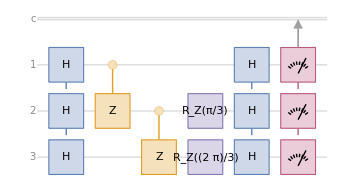

```mathematica
qc=QuantumCircuitOperator[{
"H"->{1,2,3},
"CZ"->{1,2},"CZ"->{2,3},
"RZ"[π/3]->2,"RZ"[(2π)/3]->3,
"H"->{1,2,3},
{1,2,3}
}];
qc["Diagram"]
```

Users should pay attention to specification of each QPUs, for example:

Accepted gates

Number of qubits

#### ServiceConnect

Transform the circuit into qiskit object, then decompose it:

```mathematica
qiskit=qc["Qiskit"]["Decompose"];
```

QiskitCircuit[…]

Check the qiskit circuit Diagram:

```mathematica
qiskit["Diagram"]
```

-Graphics-

Turn the Qiskit object into bytes by specifying the corresponding provider and backend on the IBM system:

```mathematica
qpy=BaseEncode@qiskit[
"QPY",
"Provider"->"IBMProvider",
"Backend"->"ibm_brisbane"
];
```

Send the circuit to an IBM QPU:

```mathematica
job1=ibmq["RunCircuit",{"QPY"->qpy,"Backend"->"ibm_brisbane"}]
```

#### QuantumCircuitOperator

With the service connection established, running a circuit can be as simple as the following code structure:

```mathematica
job2=qc[Method->{"Qiskit","Provider"->"IBMProvider","Backend"->"ibm_brisbane"}]
```

QuantumMeasurement[…]

However, this simplest method requires waiting for the job to complete and receiving a response before proceeding with any further computations. This will mean your kernel is busy waiting for a response from the hardware provider.

If you want to do other local computations while waiting for the submitted job to complete, one method is to use a separate kernel to send the request and handle the response. The following code does this and assigns the result to the variable QPU in the current kernel session:

```mathematica
LocalSubmit[
Needs["Wolfram`QuantumFramework`"];
qc[Method->{"Qiskit","Provider"->"IBMProvider","Backend"->"ibm_brisbane"}],
HandlerFunctions-><|"TaskFinished"->((job3=#EvaluationResult)&)|>
]
```

TaskObject[<|TaskUUID -> f0815d25-2f7a-4fab-8573-20733fbfff53, TaskEnvironment -> Local, TaskType -> Asynchronous, AsynchronounsTaskID -> 3, EvaluationExpression :> (Needs[Wolfram<<13>>work`]; <<1>>), <<1>>, HandlerFunctionsKeys -> {EvaluationExpression, EvaluationResult, Failure, EventName, MessageOutput, PrintOutput, Task, TaskStatus, TaskType, TaskUUID}, AutoRemove -> True|>]

Note that the wait time for QPU providers to provide responses can vary quite a lot, and is dependent on the queue for the specific backend.

### Jobs

ServiceConnect offers multiple options to explore QPU's requested jobs:

"JobResults" | Specific job result
"Jobs" | Jobs assigned to ServiceConnect object
"JobStatus" | Specific job status

Check all the jobs requested in your service:

```mathematica
ibmq["Jobs"]
```

#### Job Status

It is possible to check the specified job’s status during evaluation or when it is already finished:

```mathematica
jobStatus=ibmq["JobStatus",{"JobID"->job1["id"]}]
```

Retrieve the creation time of a job:

```mathematica
jobStatus["created"]//DateObject
```

Mon 18 Nov 2024 15:25:26GMT-5

Note that you can see the job status from your IBM-quantum account:

#### Job Results

Once the job is done, you can also check on results using the service connection and the appropriate job ID:

```mathematica
jobResult=ibmq["JobResults",{"JobID"->job1["id"]}]
```

### Results

If you already know the job is done and want to store the results, you can use the appropriate job ID and perform some post-processing to get the data into shape:

```mathematica
counts=jobResult["results",All,"data","counts"]
```

```mathematica
expResults=Normalize[N@First[Normal[Values[counts]]],Total]
```

{0.0635,0.176,0.1645,0.16875,0.07625,0.18225,0.0795,0.08925}

Calculate the theoretical results using the defined QuantumCircuitOperator:

```mathematica
theoryResults=qc[]["ProbabilityList"]//N
```

{0.0625,0.1875,0.0625,0.1875,0.1875,0.0625,0.1875,0.0625}

Plot the results and compare:

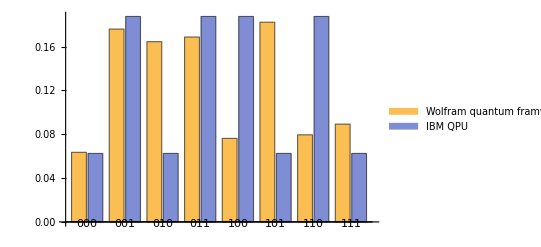

```mathematica
BarChart[Transpose[{expResults,theoryResults}],]
```

As observed, there have been some errors in the hardware, possibly due to environmental noise or other factors.

## AWS-Bracket

Using your token, you can connect to AWS:

```mathematica
aws=ServiceConnect["AWS"]
s3=ServiceExecute["AWS","GetService",{"Name"->"S3"}] 
braket=ServiceExecute["AWS","GetService",{"Name"->"Braket"}]
```

ServiceObject[…]

ServiceObject[…]

ServiceObject[…]

### Devices

Gather information about the various devices available through your service:

```mathematica
devices=braket["SearchDevices","Filters"->{}] ["Devices",All]
```

Verify the device status of each QPU:

```mathematica
devices[All,{"DeviceName","DeviceStatus"}]
```

#### QPU Properties

Check the specifications of a specific QPU device:

```mathematica
ionq=devices[1,MapAt[ImportString[#,"RawJSON"]&,"DeviceCapabilities"]]
```

### Run Quantum Circuit

There are two methods in order to run a circuit in a QPU using Wolfram Quantum Framework, using the ServiceConnect or QuantumCircuitOperator object. First of all, we need a quantum circuit:

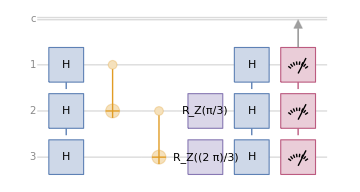

```mathematica
qc=QuantumCircuitOperator[{
"H"->{1,2,3},
"CNOT"->{1,2},"CNOT"->{2,3},
"RZ"[π/3]->2,"RZ"[(2π)/3]->3,
"H"->{1,2,3},
{1,2,3}
}];
qc["Diagram"]
```

Users should pay attention to specification of each QPUs, for example:

Accepted gates

Number of qubits

#### ServiceConnect

Transform the quantum circuit into Qiskit and find its OpenQASM code using AWSProvider:

```mathematica
qasm=qc["Qiskit"]["QASM", "Provider" -> "AWSBraket"]
```

OPENQASM 3.0;
bit[3] b;
qubit[3] q;
h q[0];
h q[1];
cnot q[0], q[1];
h q[0];
h q[2];
cnot q[1], q[2];
rz(1.0471975511965976) q[1];
h q[1];
rz(2.0943951023931953) q[2];
h q[2];
b[0] = measure q[0];
b[1] = measure q[1];
b[2] = measure q[2];

Using this OpenQASM code,  we can send the query to the Amazon simulator and our personal "OutputS3Bucket":

```mathematica
taskIonQ=braket["CreateQuantumTask",
"DeviceArn"->ionq["DeviceArn"],
"OutputS3Bucket"->"amazon-braket-wolfram-mads","OutputS3KeyPrefix"->"tasks",
"Shots"->100,"Action"-><|"braketSchemaHeader"-><|"name"->"braket.ir.openqasm.program","version"->"1"|>,
"source"->qasm|>,
"ValidateRequest"->False,"RequestRegion"->"us-east-1"]
```

### Task

Check all the jobs requested in your service:

```mathematica
taskIonQ["QuantumTaskArn"]
```

arn:aws:braket:us-east-1:153593885406:quantum-task/5fb7cfc5-d287-4f12-baa7-6e700b86c16c

Check the status of the task:

```mathematica
braket["GetQuantumTask","QuantumTaskArn"->taskIonQ["QuantumTaskArn"],"RequestRegion"->"us-east-1"]
```

#### Job Results

Once the job is done, you can also check on results:

```mathematica
braket["GetQuantumTask","QuantumTaskArn"->taskIonQ["QuantumTaskArn"],"RequestRegion"->"us-east-1"]
```

### Results

The results of the requested updates are saved in S3. We can find these by locating their directories:

```mathematica
outputPathIONQ=braket["GetQuantumTask",
"QuantumTaskArn"->taskIonQ["QuantumTaskArn"],
"RequestRegion"->"us-east-1"
]["OutputS3Directory"]
```

tasks/5fb7cfc5-d287-4f12-baa7-6e700b86c16c

Given the previous directory, the measurement result can be obtained as follows:

```mathematica
resultsIonQ=KeySort[ImportByteArray[s3["GetObject","Bucket"->"amazon-braket-wolfram-mads","Key"->outputPathIONQ<>"/"<> "results.json",
"RequestRegion"->"us-east-1"]["Body"],"RawJSON"]["measurementProbabilities"]];
```

Based on the generated results for IonQ, we can then calculate the probabilities:

```mathematica
resultsIonQ=Join[AssociationThread[StringJoin/@Tuples[{"0","1"},3],0],resultsIonQ]
```

<|000→0.14,001→0.6,010→0.08,011→0.18,100→0,101→0,110→0,111→0|>

We can then chart results for the IonQ QPU (100 shots) and the Wolfram Quantum Framework (exact probabilities as predicted by quantum theory):

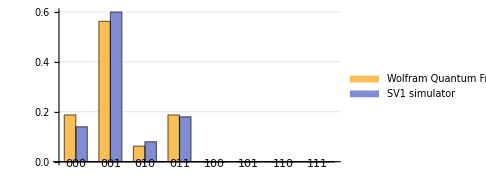

```mathematica
BarChart[Transpose[Values/@{N@qc[]["Probabilities"],resultsIonQ}],]
```

As observed, there have been some errors in the hardware, possibly due to environmental noise or other factors.

Related Guides

Related Tech Notes

## Metadata

### Categorization

Tech Note

Wolfram/QuantumFramework

Wolfram`QuantumFrameworkLoader`

Wolfram/QuantumFramework/tutorial/QPUServiceConnect

### Keywords